```mathematica
SetDirectory[NotebookDirectory[]];
cm = 72/2.54;
```

## Data Visualisation

The data set is extracted and labelled based on track selections from 2014. The tracks used in this data set have level 1 and level 2 within the global drift ranges selected by the users at the time and have value of the LDA filter > 0.01.

The positive class contains 299 tracks and the negative class contains 23915 tracks.

```mathematica
data = BinaryDeserialize[<<"data/2014-lda_gt_0.01-scores.bin"];
```

The data is centered around 0 and every dimension is scaled so that it has standard deviation of 1. This would significantly improve the training speed when the neural network is initialized with the Xavier algorithm.

```mathematica
sdata = #1-> #2&@@@Transpose[{Standardize[Keys[data], Mean, StandardDeviation],
Values[data]}];
```

There are some relationships between scores which are non-linear. Such example is change probability and duration.

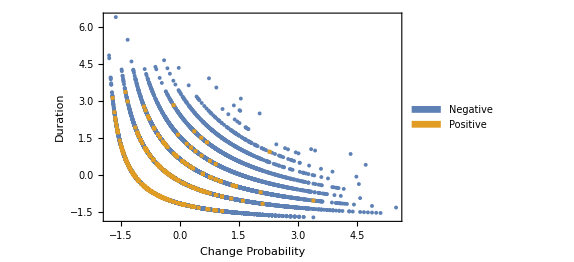

```mathematica
ListPlot[{
Keys[Select[sdata, Values@#===no&]][[All, {1,2}]],
Keys[Select[sdata, Values@#===yes&]][[All, {1,2}]]
}, PlotLegends->SwatchLegend[{"Negative", "Positive"}],
Frame-> True,
FrameLabel->{"Change Probability", "Duration"},
ImageSize->15cm,
PlotRange->All,
PlotMarkers->{Automatic, 4}
]
```

Applying PCA and projecting the data on the first two components shows large overlap between the positive and the negative class. Two principal components are not sufficient to describe the data, however further analysis shows similar overlap in the score space.

```mathematica
proj = #1->#2 &@@@ Transpose[{
#.Transpose@Eigenvectors@Covariance@#&@Keys[sdata],
Values[sdata]}];
```

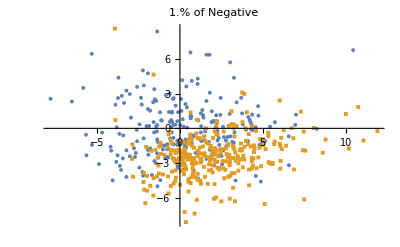
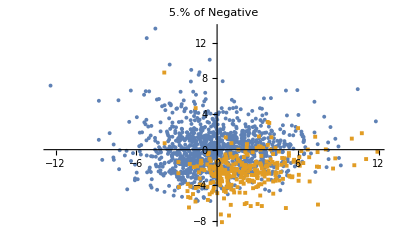
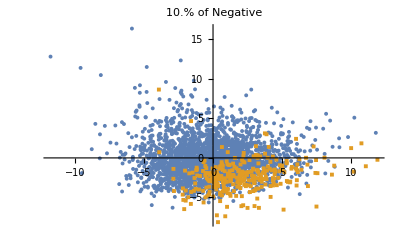
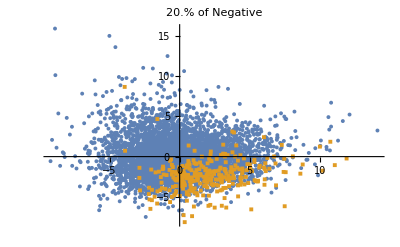
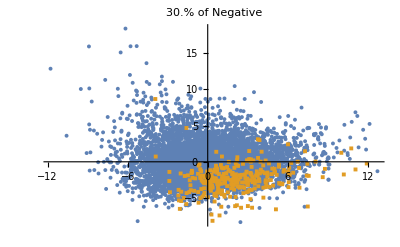
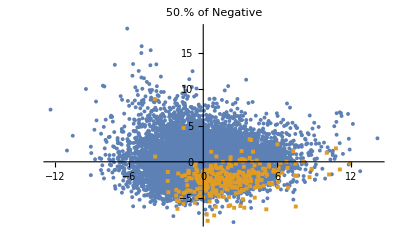
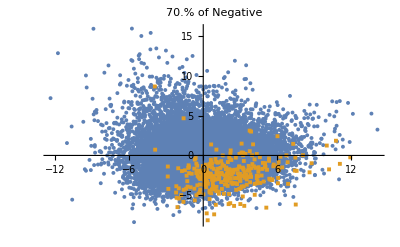
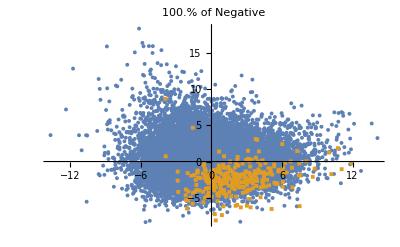
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[ArrayReshape[
Append[
Table[
ListPlot[{
Take[#, Floor[ratio Length@#]]&@RandomSample[Keys[Select[proj, Values@#===no&]][[All, 1;;2]]],
Keys[Select[proj, Values@#===yes&]][[All, 1;;2]]
},
PlotMarkers->{Automatic, 4},
PlotRange->All,
PlotLabel->ToString[100 ratio] <> "% of Negative"],
{ratio,{0.01, 0.05, 0.1, 0.2, 0.3, 0.5, 0.7,1.0}}
],
SwatchLegend[ColorData[97]/@ {1, 2}, {"Negative","Positive"}]
],
{3, 3}
]]
```

## Training Classifier on PCA compressed Data Set

Training neural network with hidden units from 1 to 10 on the full data set. The data set is projected on 2, 4, 6 ... 58 principal components. The F1Score is measured on the training and testing data set. Each trail is repeated 10 times and the data set is randomized before begin split into training and testing data. The training data is 70% and the testing data is 30%.

The results do not show any advantage in using dimensionality reduction. Even when using all 58 components there isn’t large difference between training and testing accuracy for 1 hidden unit, however it is easier to over-fit when using more than 1 hidden unit.

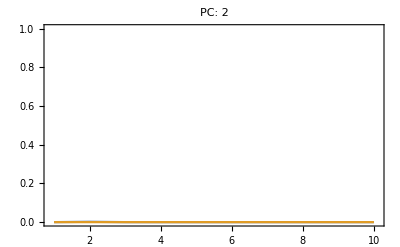
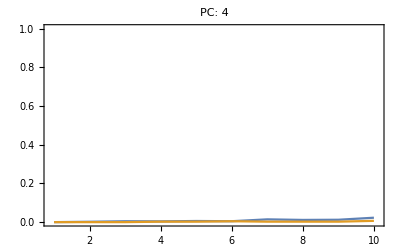
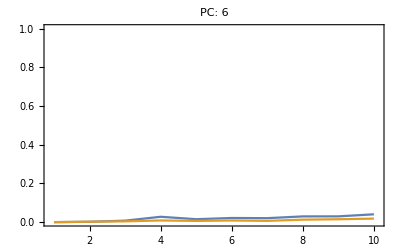
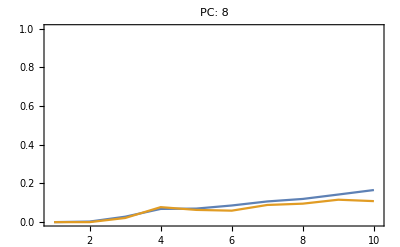
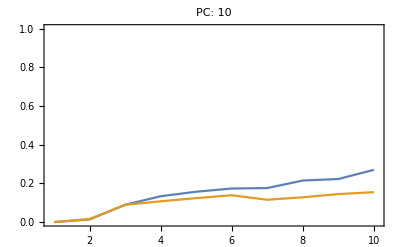
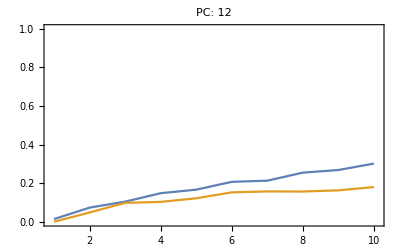
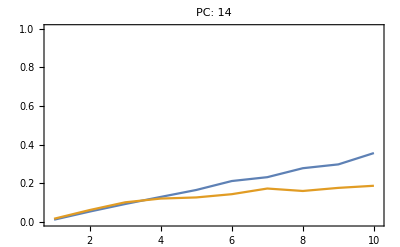
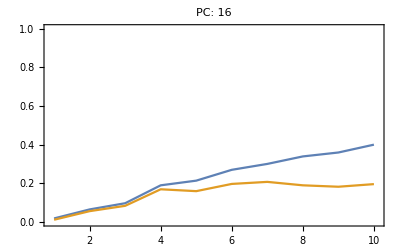
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[
ArrayReshape[
ListLinePlot[
Mean@BinaryDeserialize[
Get[
"results/nn/20180919/2014-lda_lt_0.01-scores-pca_"<>ToString[#]<>".bin"
]
],
Frame-> True,
PlotRange->{{0.9, 10.1},{0., 1.}},
PlotLabel->"PC: " <> ToString[#]
]&/@Range[2, 58, 2],
{10, 3}, Null
]
]
```

## Undersampling

Measuring the F1Score on data sets with different size of the negative class, shows that the F1Score is very sensitive to the class ratio. The F1Score is designed to handle class imbalance, and it would not be sensitive to the ratio if there is no overlap. However if there is overlap similar to the one shown on the PCA 2D projection of the data, under-sampling the negative class would change the density of negative samples in the region covered by the positive class and therefore change the false positives.

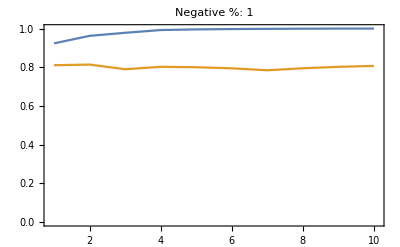
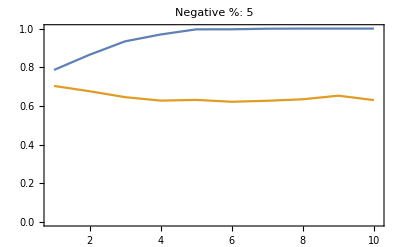
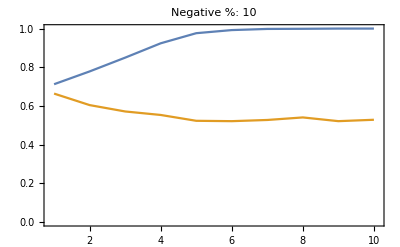
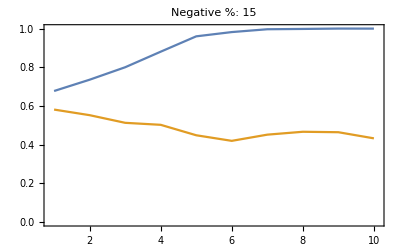
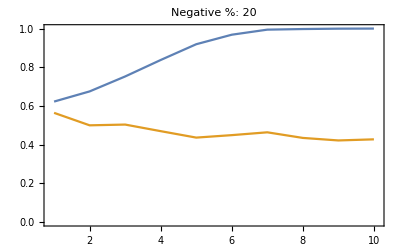
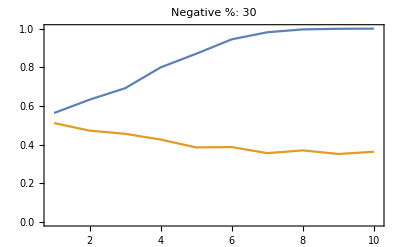
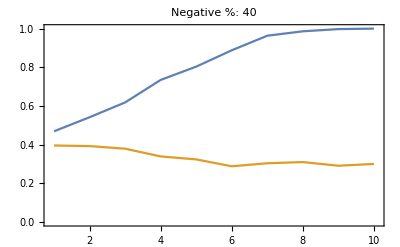
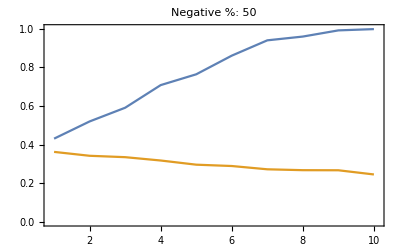
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
Grid[
ArrayReshape[
ListLinePlot[Mean@ BinaryDeserialize[
Get["results/nn-undersampling/2018-09-23_20-44-58/2014-lda_gt_0.01-scores-undersample_"<>ToString[#]<>".bin"]
],
PlotLabel->"Negative %: " <> ToString[#],
Frame-> True,
PlotRange->{{0.9, 10.1},{0.0, 1.0}}
]&/@ {1, 5, 10, 15, 20, 30, 40, 50, 60, 70, 80, 90, 100},
{5, 3}, Null]
]
```

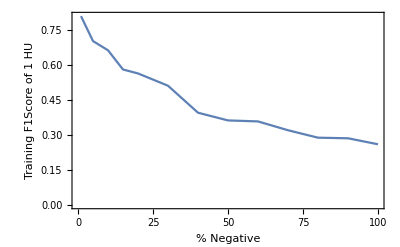

```mathematica
ListLinePlot[
Transpose[{
{1, 5, 10, 15, 20, 30, 40, 50, 60, 70, 80, 90, 100},
Mean[BinaryDeserialize[
Get["results/nn-undersampling/2018-09-23_20-44-58/2014-lda_gt_0.01-scores-undersample_"<>ToString[#]<>".bin"]
]][[2, 1]]&/@ {1, 5, 10, 15, 20, 30, 40, 50, 60, 70, 80, 90, 100}
}],
Frame->True,
FrameLabel->{"% Negative", "Training F1Score of 1 HU"}
]
```

Another reason for the low performance of the classifier for the full data set is that the neural network “ignores” the positive class, since it is very small in comparison to the negative class and would not affect the log-likelihood as much. This possibility can be confirmed or ruled out by training the classifier on the data set with under-sampled negative class and testing on the full data set. If the training and testing f1score are similar then this means that the classifier has learned the class boundaries on the under-sampled data set and has successfully classified the full data set. However if the low f1 score on the full data set is caused by an overlap, then the training and testing f1score will be very different.

The plots show training and testing data f1 score for classifier trained on different level of under-sampled negative class and tested on the full data set.

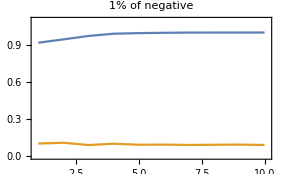
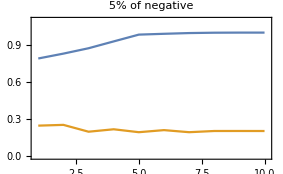
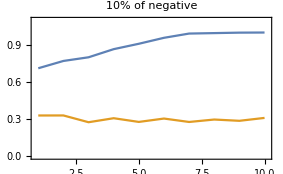
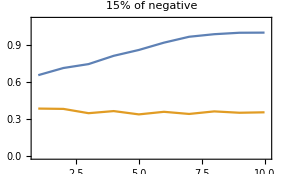
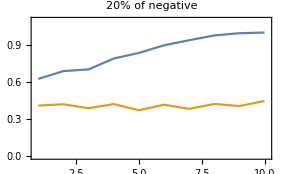
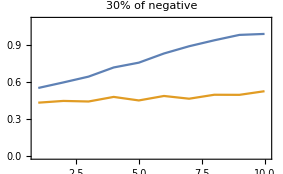
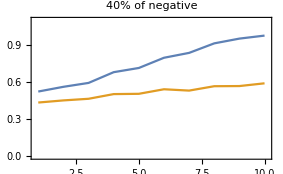
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[
ArrayReshape[
Append[
ListLinePlot[
Transpose[
Mean[
Get[
"results/nn-undersampling-test-all/2018-09-25_11-39-28/2014-lda_gt_0.01-scores-undersample-"<>ToString[#]<>".bin"]
][[All, All, 1]]
],
Frame-> True,
PlotRange->{{0.9, 10.1},{0.0, 1.1}},
PlotLabel->ToString[#]<>"% of negative",
ImageSize->10cm
]&/@ {1, 5, 10, 15, 20, 30, 40},
SwatchLegend[ColorData[97]/@{1, 2}, {"Train (Full)", "Test (Under-Sample)"}]
],
{4, 2}]
]
```

## Mislabelled Tracks

An example of mistakes made by the users is the wether the tracks go to zero after the last photo-bleaching step. The histogram shows the absolute values of the ratio between the mean and the standard deviation of the intensity in an extrapolated region of 10 frames after the last photo-bleaching step. For both classes, the positive and the negative, only ratios which are larger than 2 are shown.

Mean[I_{tend+1:tend+10}]/StandardDeviation[I_{tend+1:tend+10}]

If the tracks are properly selected then there should not be any positive tracks in that range, however there were 25 tracks out of 299 in that range, 8.36% false positive.

```mathematica
Length@Select[Abs[Keys[Select[data, Values@#===yes&]][[All,46]]], #> 2&]/299.
```

```mathematica
Length@Select[Abs[Keys[Select[data, Values@#===yes&]][[All,46]]], #> 2&]
```

38

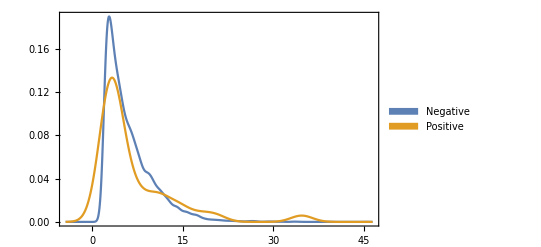

```mathematica
SmoothHistogram[{
Select[Abs[Keys[Select[data, Values@#===no&]][[All,46]]], #>2&],
Select[Abs[Keys[Select[data, Values@#===yes&]][[All,46]]], #> 2&]
},
PlotRange->All,
PlotLegends->SwatchLegend[{"Negative", "Positive"}],
Frame-> True]
```

The tracks which have ratio larger than 2 are projected on the first two principal components with different color.

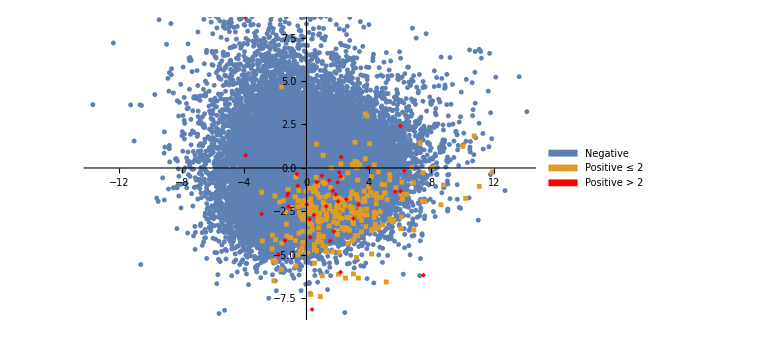

```mathematica
Block[{
sdataNegative,
sdataPositiveL2,
sdataPositiveSE2,
pc,
m,
s
},
m = Mean@Keys@data;
s = StandardDeviation@Keys@data;

pc = Transpose@Part[#, {1, 2}]&@Eigenvectors@Covariance@Keys@sdata;
sdataNegative = Keys@Select[sdata, Values@# ===no&];
{sdataPositiveL2, sdataPositiveSE2} = {
(#-m)/s&/@Select[#, Abs[#[[46]]]> 2&],
(#-m)/s&/@Select[#, Abs[#[[46]]]≤ 2&]
}&@ Keys@Select[data, Values@# ===yes&];
ListPlot[{
sdataNegative.pc,
sdataPositiveSE2.pc,
sdataPositiveL2.pc
},
PlotStyle->Append[ColorData[97]/@{1, 2}, Red],
PlotMarkers->{Automatic, 5},
ImageSize->20cm,
PlotLegends->Placed[SwatchLegend[{"Negative", "Positive ≤ 2", "Positive > 2"}],Below]]
]
```

```mathematica
Needs["DatabaseLink`"];
<<"helpers-scores.wls";
<<"helpers-data.wls";
<<"scores.wls";
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"]];
```

```mathematica
records = Select[
SmiUnpackRecords@@@
SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img
from smidata
where 
    dataset_id = 13
and category = 1
and lda_filter > 0.010"],
Abs@GoesToZero[#]>2.0&
];
```

```mathematica
Export["track_ids.csv",records[[All, {1, 2}]]];
```